Инициализация

```mathematica
import=Import["http://elib.zib.de/pub/mp-testdata/tsp/tsplib/tsp/berlin52.tsp","Data"]
```

{NAME: berlin52,TYPE: TSP,COMMENT: 52 locations in Berlin (Groetschel),DIMENSION: 52,EDGE_WEIGHT_TYPE: EUC_2D,NODE_COORD_SECTION,1 565.0 575.0,2 25.0 185.0,3 345.0 750.0,4 945.0 685.0,5 845.0 655.0,6 880.0 660.0,7 25.0 230.0,8 525.0 1000.0,9 580.0 1175.0,10 650.0 1130.0,11 1605.0 620.0 ,12 1220.0 580.0,13 1465.0 200.0,14 1530.0 5.0,15 845.0 680.0,16 725.0 370.0,17 145.0 665.0,18 415.0 635.0,19 510.0 875.0  ,20 560.0 365.0,21 300.0 465.0,22 520.0 585.0,23 480.0 415.0,24 835.0 625.0,25 975.0 580.0,26 1215.0 245.0,27 1320.0 315.0,28 1250.0 400.0,29 660.0 180.0,30 410.0 250.0,31 420.0 555.0,32 575.0 665.0,33 1150.0 1160.0,34 700.0 580.0,35 685.0 595.0,36 685.0 610.0,37 770.0 610.0,38 795.0 645.0,39 720.0 635.0,40 760.0 650.0,41 475.0 960.0,42 95.0 260.0,43 875.0 920.0,44 700.0 500.0,45 555.0 815.0,46 830.0 485.0,47 1170.0 65.0,48 830.0 610.0,49 605.0 625.0,50 595.0 360.0,51 1340.0 725.0,52 1740.0 245.0,EOF}

```mathematica
numberOfVertices=52;
```

```mathematica
points=ToExpression[Rest/@StringSplit[import⟦-numberOfVertices-1;;-2⟧]]
```

{{565.,575.},{25.,185.},{345.,750.},{945.,685.},{845.,655.},{880.,660.},{25.,230.},{525.,1000.},{580.,1175.},{650.,1130.},{1605.,620.},{1220.,580.},{1465.,200.},{1530.,5.},{845.,680.},{725.,370.},{145.,665.},{415.,635.},{510.,875.},{560.,365.},{300.,465.},{520.,585.},{480.,415.},{835.,625.},{975.,580.},{1215.,245.},{1320.,315.},{1250.,400.},{660.,180.},{410.,250.},{420.,555.},{575.,665.},{1150.,1160.},{700.,580.},{685.,595.},{685.,610.},{770.,610.},{795.,645.},{720.,635.},{760.,650.},{475.,960.},{95.,260.},{875.,920.},{700.,500.},{555.,815.},{830.,485.},{1170.,65.},{830.,610.},{605.,625.},{595.,360.},{1340.,725.},{1740.,245.}}

Заготовка для алгоритма

```mathematica
distanceMatrix=N@DistanceMatrix[points];
```

```mathematica
v=Range@numberOfVertices;
```

```mathematica
a=Apply[UndirectedEdge,Subsets[v,{2}],{1}];
```

```mathematica
First@FindHamiltonianCycle[a,2]
```

{1<->51,51<->3,3<->49,49<->5,5<->47,47<->7,7<->45,45<->9,9<->43,43<->11,11<->41,41<->13,13<->39,39<->15,15<->37,37<->17,17<->35,35<->19,19<->33,33<->21,21<->31,31<->23,23<->29,29<->25,25<->27,27<->26,26<->28,28<->24,24<->30,30<->22,22<->32,32<->20,20<->34,34<->18,18<->36,36<->16,16<->38,38<->14,14<->40,40<->12,12<->42,42<->10,10<->44,44<->8,8<->46,46<->6,6<->48,48<->4,4<->50,50<->2,2<->52,52<->1}

```mathematica
start=RandomSample[v]
```

{46,11,51,50,42,14,48,45,27,47,49,12,17,22,13,28,18,26,3,32,1,38,52,44,39,20,30,34,15,23,4,5,10,19,2,43,36,6,21,33,25,24,37,9,40,16,35,31,41,7,29,8}

```mathematica
distance=Total@Table[distanceMatrix⟦start⟦i⟧,start⟦i+1⟧⟧,{i,numberOfVertices-1}]+distanceMatrix⟦start⟦-1⟧,start⟦1⟧⟧
```

29443.3

```mathematica
t=25;
α=0.85;
```

```mathematica
elem1=RandomChoice[v]
elem2=RandomChoice[Delete[v,elem1]]
elems={elem1,elem2}
```

28

3

{28,3}

Первый метод

```mathematica
newStart1=start;
newStart1⟦Min@elems;;Max@elems⟧=Reverse@newStart1⟦Min@elems;;Max@elems⟧;
```

```mathematica
newStart1
```

{46,11,34,30,20,39,44,52,38,1,32,3,26,18,28,13,22,17,12,49,47,27,45,48,14,42,50,51,15,23,4,5,10,19,2,43,36,6,21,33,25,24,37,9,40,16,35,31,41,7,29,8}

```mathematica
newDistance1=Total@Table[distanceMatrix⟦newStart1⟦i⟧,newStart1⟦i+1⟧⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart1⟦-1⟧,newStart1⟦1⟧⟧
```

30385.1

Второй метод

```mathematica
newStart2=start;
del=newStart2⟦elem1⟧;
newStart2=Delete[newStart2,elem1];
newStart2=Insert[newStart2,del,elem2];
```

```mathematica
newStart2
```

{46,11,34,51,50,42,14,48,45,27,47,49,12,17,22,13,28,18,26,3,32,1,38,52,44,39,20,30,15,23,4,5,10,19,2,43,36,6,21,33,25,24,37,9,40,16,35,31,41,7,29,8}

```mathematica
newDistance2=Total@Table[distanceMatrix⟦newStart2⟦i⟧,newStart2⟦i+1⟧⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart2⟦-1⟧,newStart2⟦1⟧⟧
```

30716.6

Третий метод

```mathematica
newStart3=start;
temp=newStart3⟦elem2⟧;
newStart3⟦elem2⟧=newStart3⟦elem1⟧;
newStart3⟦elem1⟧=temp;
```

```mathematica
newStart3
```

{46,11,51,50,42,14,48,45,27,47,49,12,17,22,13,28,18,26,3,32,1,38,52,44,2,20,30,34,15,23,4,5,10,19,39,43,36,6,21,33,25,24,37,9,40,16,35,31,41,7,29,8}

```mathematica
newDistance3=Total@Table[distanceMatrix⟦newStart3⟦i⟧,newStart3⟦i+1⟧⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart3⟦-1⟧,newStart3⟦1⟧⟧
```

28978.6

Процедура выбора пути

```mathematica
starts={newStart1,newStart2,newStart3};
distances={newDistance1,newDistance2,newDistance3};
```

```mathematica
minimal=Min@distances
```

28978.6

```mathematica
pos=Position[distances,minimal]⟦1,1⟧
```

3

```mathematica
start=If[Which[distance≥ minimal,True,distance< minimal,RandomReal[]<E^((-(minimal-distance))/t)],starts⟦pos⟧,start]
```

{46,11,51,50,42,14,48,45,27,47,49,12,17,22,13,28,18,26,3,32,1,38,52,44,2,20,30,34,15,23,4,5,10,19,39,43,36,6,21,33,25,24,37,9,40,16,35,31,41,7,29,8}

```mathematica
t=α t
```

21.25

Алгоритм

```mathematica
simulatedAnnealing[points_,t_,α_,iter_]:=Module[{distanceMatrix=N@DistanceMatrix[points],numberOfVertices=Length@points,newt=t,v,start,distance,elem1,elem2,elems,newStart1,newStart2,newStart3,newDistance1,newDistance2,newDistance3,del,temp,starts,distances,minimal,pos},
v=Range@numberOfVertices;
start=RandomSample[v];
Do[distance=Total@Table[distanceMatrix⟦start⟦i⟧,start⟦i+1⟧⟧,{i,numberOfVertices-1}]+distanceMatrix⟦start⟦-1⟧,start⟦1⟧⟧;
elem1=RandomChoice[v];
elem2=RandomChoice[Delete[v,elem1]];
elems={elem1,elem2};
newStart1=start;
newStart1⟦Min@elems;;Max@elems⟧=Reverse@newStart1⟦Min@elems;;Max@elems⟧;
newDistance1=Total@Table[distanceMatrix⟦newStart1⟦i⟧,newStart1⟦i+1⟧⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart1⟦-1⟧,newStart1⟦1⟧⟧;
newStart2=start;
del=newStart2⟦elem1⟧;
newStart2=Delete[newStart2,elem1];
newStart2=Insert[newStart2,del,elem2];
newDistance2=Total@Table[distanceMatrix⟦newStart2⟦i⟧,newStart2⟦i+1⟧⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart2⟦-1⟧,newStart2⟦1⟧⟧;
newStart3=start;
temp=newStart3⟦elem2⟧;
newStart3⟦elem2⟧=newStart3⟦elem1⟧;
newStart3⟦elem1⟧=temp;
newDistance3=Total@Table[distanceMatrix⟦newStart3⟦i⟧,newStart3⟦i+1⟧⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart3⟦-1⟧,newStart3⟦1⟧⟧;
starts={newStart1,newStart2,newStart3};
distances={newDistance1,newDistance2,newDistance3};
minimal=Min@distances;
pos=Position[distances,minimal]⟦1,1⟧;
start=If[Which[distance≥ minimal,True,distance< minimal,RandomReal[]<E^((-(minimal-distance))/newt)],starts⟦pos⟧,start];
newt=α newt,{k,iter}];{Min@{distance,minimal},start}]
```

Численные результаты

```mathematica
solution=simulatedAnnealing[points,2000,0.99,5000]
```

General::munfl: Exp[-725.601] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-734.784] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-877.868] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{7544.37,{48,38,37,40,39,36,35,34,44,46,16,29,50,20,23,30,2,7,42,21,17,3,18,31,22,1,49,32,45,19,41,8,9,10,43,33,51,11,52,14,13,47,26,27,28,12,25,4,6,15,5,24}}

```mathematica
MapAt[N,FindShortestTour[points],1]
```

{7544.37,{1,49,32,45,19,41,8,9,10,43,33,51,11,52,14,13,47,26,27,28,12,25,4,6,15,5,24,48,38,37,40,39,36,35,34,44,46,16,29,50,20,23,30,2,7,42,21,17,3,18,31,22,1}}

Решение совпало с FindShortestTour

```mathematica
final=solution⟦2⟧
```

{48,38,37,40,39,36,35,34,44,46,16,29,50,20,23,30,2,7,42,21,17,3,18,31,22,1,49,32,45,19,41,8,9,10,43,33,51,11,52,14,13,47,26,27,28,12,25,4,6,15,5,24}

Визуализация

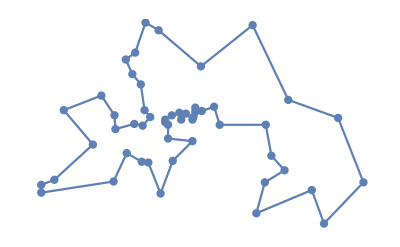

```mathematica
ListLinePlot[points⟦final⟧,Mesh->All,Axes->False]
```

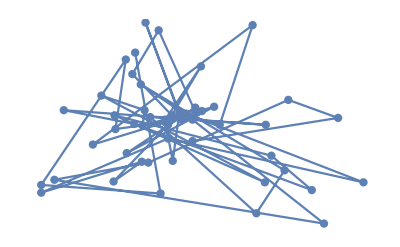

```mathematica
ListLinePlot[points⟦start⟧,Mesh->All,Axes->False]
```